```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\HILL\Documents\GitHub\thesis\figures\jitter

```mathematica
data=Import["discharge_sample.csv","Dataset",HeaderLines->1];
```

```mathematica
t=Normal[data[All,"t"]];
ch1=Normal[data[All,"ch1"]];
ch2=Normal[data[All,"ch2"]];
```

```mathematica
fontsize=50;dT=Directive[Thick];tick=0.07;thickness=0.008;
```

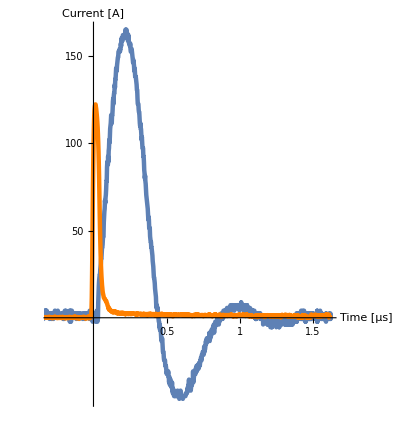

```mathematica
plot=ListLinePlot[{Thread[{t,ch1}],Thread[{t,ch2}]},
PlotRange->{{-3*^-7,Max[t]},All},
PlotStyle->{{Thickness[thickness]},{Thickness[thickness],Orange}},
TicksStyle->{{Black,FontSize->fontsize},{Black,FontSize->fontsize}},
AxesLabel->{Style["Time\n[µs]",Black,FontSize->fontsize],Style["Current [A]",Black,FontSize->fontsize]},
AxesStyle->{{Black,Thickness[0.006]},{Black,Thickness[0.006]}},
Ticks->{{{5*^-7,0.5,tick,Directive[Thickness[thickness]]},{1*^-6,1,tick,Directive[Thickness[thickness]]},{1.5*^-6,1.5,tick,Directive[Thickness[thickness]]}},{{5,50,tick,Directive[Thickness[thickness]]},{10,100,tick,Directive[Thickness[thickness]]},{15,150,tick,Directive[Thickness[thickness]]}}}
,ImageSize->Full,
AspectRatio->1/0.9]
```

```mathematica
Export["discharge_sample.pdf",plot](*or pdf as the extension.*)
```

discharge_sample.pdf

```mathematica
SystemOpen["discharge_sample.pdf"]
```